# Wilcoxon Signed Rank Distribution

## Moment Generating Function

As described in the textbook on p.393, the moment generating function for the Wilcoxon signed rank statistic is a product of moment generating functions for random variables which take the values k and -k with equal probability and k ranges from 1 to the sample size.  This is because the statistic is a sum of independent signed ranks, with the signs being +1 or -1 with probability 0.5.   For example, if the sample size is 3, the next cell gives the moment generating function of the signed rank statistic. Try changing n for a values and observe different outputs.  Make sure that you understand why the moment generating function takes this form.

```mathematica
Expand[Product[(Exp[-i*t]+Exp[i*t])/2,{i,1,3}]]
```

1/4+ⅇ^(-6 t)/8+ⅇ^(-4 t)/8+ⅇ^(-2 t)/8+ⅇ^(2 t)/8+ⅇ^(4 t)/8+ⅇ^(6 t)/8

This can be automated in a function of the sample size, mgfSignedRank, as follows:

```mathematica
mgfSignedRank[n_]:=Expand[Product[(Exp[-i*t]+Exp[i*t])/2,{i,1,n}]]
```

To check that it works:

```mathematica
mgfSignedRank[3]
```

1/4+ⅇ^(-6 t)/8+ⅇ^(-4 t)/8+ⅇ^(-2 t)/8+ⅇ^(2 t)/8+ⅇ^(4 t)/8+ⅇ^(6 t)/8

The moment generating functions have many terms for larger n:

```mathematica
mgfSignedRank[10]
```

ⅇ^(-55 t)/1024+ⅇ^(-53 t)/1024+ⅇ^(-51 t)/1024+ⅇ^(-49 t)/512+ⅇ^(-47 t)/512+(3 ⅇ^(-45 t))/1024+ⅇ^(-43 t)/256+(5 ⅇ^(-41 t))/1024+(3 ⅇ^(-39 t))/512+ⅇ^(-37 t)/128+(5 ⅇ^(-35 t))/512+(11 ⅇ^(-33 t))/1024+(13 ⅇ^(-31 t))/1024+(15 ⅇ^(-29 t))/1024+(17 ⅇ^(-27 t))/1024+(5 ⅇ^(-25 t))/256+(11 ⅇ^(-23 t))/512+(3 ⅇ^(-21 t))/128+(27 ⅇ^(-19 t))/1024+(29 ⅇ^(-17 t))/1024+(31 ⅇ^(-15 t))/1024+(33 ⅇ^(-13 t))/1024+(35 ⅇ^(-11 t))/1024+(9 ⅇ^(-9 t))/256+(19 ⅇ^(-7 t))/512+(39 ⅇ^(-5 t))/1024+(39 ⅇ^(-3 t))/1024+(5 ⅇ^-t)/128+(5 ⅇ^t)/128+(39 ⅇ^(3 t))/1024+(39 ⅇ^(5 t))/1024+(19 ⅇ^(7 t))/512+(9 ⅇ^(9 t))/256+(35 ⅇ^(11 t))/1024+(33 ⅇ^(13 t))/1024+(31 ⅇ^(15 t))/1024+(29 ⅇ^(17 t))/1024+(27 ⅇ^(19 t))/1024+(3 ⅇ^(21 t))/128+(11 ⅇ^(23 t))/512+(5 ⅇ^(25 t))/256+(17 ⅇ^(27 t))/1024+(15 ⅇ^(29 t))/1024+(13 ⅇ^(31 t))/1024+(11 ⅇ^(33 t))/1024+(5 ⅇ^(35 t))/512+ⅇ^(37 t)/128+(3 ⅇ^(39 t))/512+(5 ⅇ^(41 t))/1024+ⅇ^(43 t)/256+(3 ⅇ^(45 t))/1024+ⅇ^(47 t)/512+ⅇ^(49 t)/512+ⅇ^(51 t)/1024+ⅇ^(53 t)/1024+ⅇ^(55 t)/1024

## Probabilities

For n=3, the values that the signed rank sum can take are {-6, -4, -2, 0, 2, 4, 6}.The probabilities for the signed rank statistic taking its valuesare the coefficients of the terms {e^(-6t), ..., e^(6t)} .  In order to use Mathematica’ s abilities to pick off coefficients of polynomials, it is better to substitute x for e^t.To make the resulting expression into a polynomial (so that the lowest power is x^0), it is necessary to multiply by x^6. For a general sample size n, this involves multiplying by x^(n(n+1)/2).  Try changing n for a values and observe different outputs. Make sure that you understand why this works.

```mathematica
polySignedRank[n_] := Expand[x^(n*(n+1)/2)*Product[(x^(-i)+x^i)/2,{i,1,n}]]
```

```mathematica
polySignedRank[3]
```

1/8+x^2/8+x^4/8+x^6/4+x^8/8+x^10/8+x^12/8

```mathematica
polySignedRank[10]
```

1/1024+x^2/1024+x^4/1024+x^6/512+x^8/512+(3 x^10)/1024+x^12/256+(5 x^14)/1024+(3 x^16)/512+x^18/128+(5 x^20)/512+(11 x^22)/1024+(13 x^24)/1024+(15 x^26)/1024+(17 x^28)/1024+(5 x^30)/256+(11 x^32)/512+(3 x^34)/128+(27 x^36)/1024+(29 x^38)/1024+(31 x^40)/1024+(33 x^42)/1024+(35 x^44)/1024+(9 x^46)/256+(19 x^48)/512+(39 x^50)/1024+(39 x^52)/1024+(5 x^54)/128+(5 x^56)/128+(39 x^58)/1024+(39 x^60)/1024+(19 x^62)/512+(9 x^64)/256+(35 x^66)/1024+(33 x^68)/1024+(31 x^70)/1024+(29 x^72)/1024+(27 x^74)/1024+(3 x^76)/128+(11 x^78)/512+(5 x^80)/256+(17 x^82)/1024+(15 x^84)/1024+(13 x^86)/1024+(11 x^88)/1024+(5 x^90)/512+x^92/128+(3 x^94)/512+(5 x^96)/1024+x^98/256+(3 x^100)/1024+x^102/512+x^104/512+x^106/1024+x^108/1024+x^110/1024

The command CoefficientList (look at the help for this command) then extracts the coefficients of the polynomials which are the probabilities of the values {-n(n+1)/2,..., n(n+1)/2}.  Every second coefficient is 0, that is the corresponding probability is 0. Why?

```mathematica
CoefficientList[polySignedRank[3],x]
```

{1/8,0,1/8,0,1/8,0,1/4,0,1/8,0,1/8,0,1/8}

```mathematica
CoefficientList[polySignedRank[10],x]
```

{1/1024,0,1/1024,0,1/1024,0,1/512,0,1/512,0,3/1024,0,1/256,0,5/1024,0,3/512,0,1/128,0,5/512,0,11/1024,0,13/1024,0,15/1024,0,17/1024,0,5/256,0,11/512,0,3/128,0,27/1024,0,29/1024,0,31/1024,0,33/1024,0,35/1024,0,9/256,0,19/512,0,39/1024,0,39/1024,0,5/128,0,5/128,0,39/1024,0,39/1024,0,19/512,0,9/256,0,35/1024,0,33/1024,0,31/1024,0,29/1024,0,27/1024,0,3/128,0,11/512,0,5/256,0,17/1024,0,15/1024,0,13/1024,0,11/1024,0,5/512,0,1/128,0,3/512,0,5/1024,0,1/256,0,3/1024,0,1/512,0,1/512,0,1/1024,0,1/1024,0,1/1024}

To get the probability distribution, the values need to be associated with the probabilities and stored in a list of pairs.  For sample size n, the number of values is n(n+1) + 1.  The command Table allows us to associate the values to the probabilities and automate it in a function. Try changing n for a values and observe different outputs.

```mathematica
pdfSignedRank[n_]:=Table[{i-1-n*(n+1)/2,
CoefficientList[polySignedRank[n],x][[i]]},{i,1,n*(n+1)+1}]
```

```mathematica
pdfSignedRank[3]
```

{{-6,1/8},{-5,0},{-4,1/8},{-3,0},{-2,1/8},{-1,0},{0,1/4},{1,0},{2,1/8},{3,0},{4,1/8},{5,0},{6,1/8}}

```mathematica
pdfSignedRank[10]
```

{{-55,1/1024},{-54,0},{-53,1/1024},{-52,0},{-51,1/1024},{-50,0},{-49,1/512},{-48,0},{-47,1/512},{-46,0},{-45,3/1024},{-44,0},{-43,1/256},{-42,0},{-41,5/1024},{-40,0},{-39,3/512},{-38,0},{-37,1/128},{-36,0},{-35,5/512},{-34,0},{-33,11/1024},{-32,0},{-31,13/1024},{-30,0},{-29,15/1024},{-28,0},{-27,17/1024},{-26,0},{-25,5/256},{-24,0},{-23,11/512},{-22,0},{-21,3/128},{-20,0},{-19,27/1024},{-18,0},{-17,29/1024},{-16,0},{-15,31/1024},{-14,0},{-13,33/1024},{-12,0},{-11,35/1024},{-10,0},{-9,9/256},{-8,0},{-7,19/512},{-6,0},{-5,39/1024},{-4,0},{-3,39/1024},{-2,0},{-1,5/128},{0,0},{1,5/128},{2,0},{3,39/1024},{4,0},{5,39/1024},{6,0},{7,19/512},{8,0},{9,9/256},{10,0},{11,35/1024},{12,0},{13,33/1024},{14,0},{15,31/1024},{16,0},{17,29/1024},{18,0},{19,27/1024},{20,0},{21,3/128},{22,0},{23,11/512},{24,0},{25,5/256},{26,0},{27,17/1024},{28,0},{29,15/1024},{30,0},{31,13/1024},{32,0},{33,11/1024},{34,0},{35,5/512},{36,0},{37,1/128},{38,0},{39,3/512},{40,0},{41,5/1024},{42,0},{43,1/256},{44,0},{45,3/1024},{46,0},{47,1/512},{48,0},{49,1/512},{50,0},{51,1/1024},{52,0},{53,1/1024},{54,0},{55,1/1024}}

## PDF Plots

The pdf for the Wilcoxon signed rank statistic can be plotted using the ListPlot (look at the help) command.  Try changing n for a values and observe different outputs.

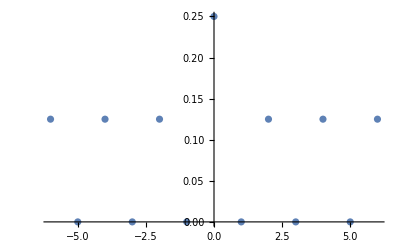

```mathematica
ListPlot[pdfSignedRank[3]]
```

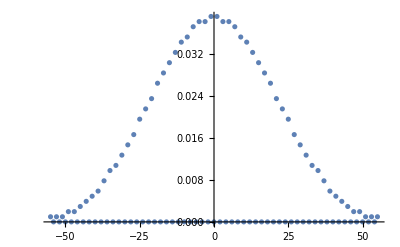

```mathematica
ListPlot[pdfSignedRank[10]]
```

## Distribution for the Wilcoxon Signed Rank Statistic

The Mathematica command EmpiricalDistribution enables us to take the table of values and probabilities that has been computed and turn it into a probability distribution on which the commands, PDF,CDF, MomentGeneratingFunction, Mean and Variance will work.  Here is the function that automates this for each sample size:

```mathematica
probDistributionSignedRank[n_] :=EmpiricalDistribution[Transpose[pdfSignedRank[n]][[2]]->Transpose[pdfSignedRank[n]][[1]]]
```

The following commands illustrate how we can get these for a specific value of the sample size n.  Try changing n for a values and observe different outputs.

```mathematica
CDF[probDistributionSignedRank[3],x]
```

1/8 Boole[-6≤x]+1/8 Boole[-4≤x]+1/8 Boole[-2≤x]+1/4 Boole[0≤x]+1/8 Boole[2≤x]+1/8 Boole[4≤x]+1/8 Boole[6≤x]

```mathematica
PDF[probDistributionSignedRank[3],x]
```

1/8 Boole[-6==x]+1/8 Boole[-4==x]+1/8 Boole[-2==x]+1/4 Boole[0==x]+1/8 Boole[2==x]+1/8 Boole[4==x]+1/8 Boole[6==x]

```mathematica
MomentGeneratingFunction[probDistributionSignedRank[3],t]
```

1/4+ⅇ^(-6 t)/8+ⅇ^(-4 t)/8+ⅇ^(-2 t)/8+ⅇ^(2 t)/8+ⅇ^(4 t)/8+ⅇ^(6 t)/8

Here is a plot of the pdf for three different values of n.  What do the distributions look like?

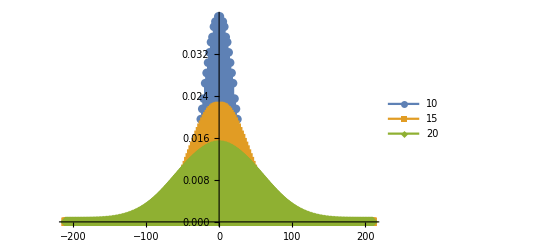

```mathematica
DiscretePlot[Table[PDF[probDistributionSignedRank[n],x],{n,{10,15,20}}]//Evaluate,{x,-210,210},PlotRange->All,PlotMarkers->Automatic,PlotLegends->{10,15,20}]
```

## Exact Evaluation in Module 8

In Module 8, we discussed the example of the lengths of n=10 sunfish.  The p-value is the probability of the value we obtained for the Wilcoxon signed rank statistic, 25, or data that would favour the alternative more.  The is 1 - the CDF for 24 which is:

```mathematica
1-CDF[probDistributionSignedRank[10],24]
```

119/1024

and in decimals this agrees with the value in R:

```mathematica
N[1-CDF[probDistributionSignedRank[10],24]]
```

0.116211

It is also easy to get the critical value by choosing the 95%tile of the distribution:

```mathematica
c=Quantile[probDistributionSignedRank[10],0.95]
```

33

and then checking what probability is to the right of this:

```mathematica
N[1-CDF[probDistributionSignedRank[10],{c-2,c-1,c}]]
```

{0.0527344,0.0527344,0.0419922}

Notice that the first two probablities are the same because 32 is not a possible value.